# Dynamic motion of lablets with sensor and actor operations

### Abhishek Sharma BioMIP RUB

## Description

Each Lablet act as a finite state machine, which has following information,

{x,y,θ,cnt,C_type,C_op,𝒞_1,𝒞_2}

{x,y,θ}  :  coordinates and orientation of Lablet
cnt : current time counter
C_type : current operation type : {1,2,3,4} 
C_op : current operation (transalational and rotational)
𝒞_1,𝒞_2 : recorded concentration via sensor

```mathematica
ClearAll["Global`*"]
```

#### Simulation parameters

```mathematica
LenX=10000; (* Simulation length along X axis *)
```

```mathematica
LenY=10000;(* Simulation length along Y axis *)
```

```mathematica
nx=100;(* Number of steps in space(x) *)
```

```mathematica
ny=100;(* Number of steps in space(y) *)
```

```mathematica
nop=20;(* Number of Lablets *)
```

```mathematica
iPos=RandomReal[{20,80},{nop,2}];(* Initializing position of lablet *)
```

```mathematica
iθ= RandomReal[{0,2π},{nop}];(* Initial orientation of lablet *)
```

```mathematica
tT=50;(* Total time of simulation *)
```

```mathematica
dt=1.;(* Time step for simulation *)
```

```mathematica
Kc=0.001;(* Rate of dissipation of chemical in surrounding *)
```

```mathematica
tSteps=nt=IntegerPart[tT/dt]; (* Total number of simulation steps *)
```

```mathematica
dx=2/(nx-1);(* Width of space step(x) *)
```

```mathematica
dy=2/(ny-1);(*Width of space step(y) *)
```

```mathematica
θR=0;(* Maximum random change in angle per time step *)
```

```mathematica
ΔxR=0.;(* Maximum random displacement along X per time step *)
```

```mathematica
ΔyR=0.;(* Maximum random displacement along Y per time step *)
```

```mathematica
ΔcR=0.1;(* Maximun noise noise in sensor measurement *)
```

```mathematica
Δt=3;(* Switching times for Lablet, also time step *)
```

```mathematica
x=Range[0,1000,dx]; (* Grid points along X *)
```

```mathematica
y=Range[0,1000,dy]; (* Grid points along Y *)
```

```mathematica
u=Table[0,{nx},{ny}]; (* Preallocating u *)
```

```mathematica
un=Table[0,{nx},{ny}]; (* Preallocating un *)
```

```mathematica
Dc=0.002;(* Diffusion coefficient *)
```

```mathematica
vLablet=0.05;ωLablet=0.05;α=π/12; (* Translational, angular velocitie and design parameter *)
```

```mathematica
ntS=2; (* Number of steps after with sensing operation takes place *)
```

```mathematica
nOp=(tT/Δt); (* Total number of switching operations  *)
```

```mathematica
noS=IntegerPart[(Δt/dt)];(* Number of steps for each thrust operation *)
```

```mathematica
nosS=IntegerPart[(Δt/dt)ntS];(* Number of time steps after which sensing takes place *)
```

```mathematica
stSeq1={0,0,0,0,0}; (* Standard translational sequence *)
```

```mathematica
stSeq2={1,1};(* Standard rotational sequence *)
```

```mathematica
seqX1={1};(* Operation for Case : C1 > C2 *)
```

```mathematica
seqX2={1,1,1};(* Operation for Case : C1 < C2 *)
```

```mathematica
u=Table[0,{nx},{ny}]; (* Preallocating u *)
un=Table[0,{nx},{ny}];(* Preallocating un *)
```

```mathematica
maxOp1=noS Length[stSeq1];
```

```mathematica
maxOp2=noS Length[stSeq2];
```

```mathematica
maxOp3=noS Length[seqX1];
```

```mathematica
maxOp4=noS Length[seqX2];
```

Defining boundary conditions

```mathematica
UW=0.; (* x=0 Dirichlet B.C. *)
UE=0.; (* x=L Dirichlet B.C. *)
US=0.; (* y=0 Dirichlet B.C. *)
UN=0.; (* y=L Dirichlet B.C. *)
```

```mathematica
bc=Table[0,{nx-2},{ny-2}];
```

```mathematica
bc⟦1,All⟧= UW/dx^2;
bc⟦nx-2,All⟧=UE/dy^2;
bc⟦All,1⟧= US/dx^2;
bc⟦All,ny-2⟧= US/dy^2;
```

```mathematica
bc⟦1,1⟧=UW/dx^2+US/dy^2;
bc⟦nx-2,1⟧=UE/dx^2+US/dy^2;
bc⟦1,ny-2⟧=UW/dx^2+UN/dy^2;bc⟦nx-2,ny-2⟧=UE/dx^2+UN/dy^2;
```

```mathematica
bc=Dc dt bc;
```

Calculating sparse matrix for implicit finite difference scheme

```mathematica
Ax=SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1},{nx-2,nx-2}];
```

```mathematica
Ay=SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1},{ny-2,ny-2}];
```

```mathematica
A=KroneckerProduct[Ay/dy^2,SparseArray[{i_,i_}->1,{nx-2,nx-2}]]+KroneckerProduct[SparseArray[{i_,i_}->1,{ny-2,ny-2}],Ax/dx^2];
```

```mathematica
Dmat=SparseArray[{i_,i_}->1,{(nx-2)(ny-2),(nx-2)(ny-2)}]-Dc dt A-Kc dt A
```

SparseArray[…]

```mathematica
iDmat=Inverse[Dmat];
```

```mathematica
posL[{x_,y_,θ_}]:=(nx-2)(y-2) +x-1
```

```mathematica
mType1[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+θR RandomReal[NormalDistribution[0,1]];
X1=X+2vLablet Cos[Θ1]dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+2vLablet Sin[Θ1]dt+ΔyR RandomReal[NormalDistribution[0,1]];
Which[X1≤ 0,X1=X1+nx,Y1≤ 0,Y1=Y1+ny,X1>nx,X1=X1-nx,Y1>ny,Y1=Y1-ny];
(*dataPos=Join[dataPos,{{X1,Y1,Θ1}}];*)
{X1,Y1,Θ1}];
```

```mathematica
mType2[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+ωLablet dt+θR RandomReal[NormalDistribution[0,1]];
X1=X+vLablet( Cos[Θ](1+Sin[α])-Cos[α]Sin[Θ])dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+vLablet( Cos[α]Cos[Θ]+(1+Sin[α])Sin[Θ])dt+ΔyR RandomReal[NormalDistribution[0,1]];
Which[X1≤ 0,X1=X1+nx,Y1≤ 0,Y1=Y1+ny,X1>nx,X1=X1-nx,Y1>ny,Y1=Y1-ny];
(*dataPos=Join[dataPos,{{X1,Y1,Θ1}}];*)
{X1,Y1,Θ1}];
```

```mathematica
seq= Flatten[ConstantArray[{1,0,0,0,0,0,0,0},{15}]];
```

```mathematica
noX=Length[seq];
```

```mathematica
pos=MapThread[Flatten[{Round[#1],#2}]&,{iPos,iθ}];
```

```mathematica
dataPos={pos};data={};
```

```mathematica
arrPos=Table[0,{(nx-2) (ny-2)}];
```

```mathematica
posList=posL[pos⟦#⟧]&/@Range[nop/2]
```

{6834,5445,5751,4755,5832,1832,3197,2882,1929,4927}

```mathematica
(arrPos⟦posL[#]⟧= 5.0)&/@pos;
```

```mathematica
U=Take[un,{2,-2},{2,-2}];U=Flatten[U+bc];
```

```mathematica
LabletState= MapThread[Flatten[{#1,#2,0,0,1,0.,0.,0.}]&,{iPos,iθ}];
```

```mathematica
LabletData={LabletState};
```

```mathematica
posL[#]&/@Round[LabletState⟦1;;nop/2,1;;3⟧]
```

{6834,5445,5751,4755,5832,1832,3197,2882,1929,4927}

```mathematica
nt=1;Monitor[While[nt≤5000,
un=u;data=Join[data,{u}];
dataIntp=u;
arrPos=Table[0,{(nx-2) (ny-2)}];
intp=Interpolation[Flatten[Table[{{i,j},dataIntp⟦i,j⟧},{i,1,nx},{j,1,ny}],1]];

(* Sensing and motion operations *)
For[i=1,i≤nop,i++,
Which[LabletState⟦i,5⟧== 0,LabletState⟦i,1;;3⟧=mType1[LabletState⟦i,1;;3⟧],LabletState⟦i,5⟧== 1,LabletState⟦i,1;;3⟧=mType2[LabletState⟦i,1;;3⟧]];
LabletState⟦i,4⟧=LabletState⟦i,4⟧+1;
LabletState⟦i,7⟧=intp[LabletState⟦i,1⟧,LabletState⟦i,2⟧];
Which[LabletState⟦i,5⟧== 0&&LabletState⟦i,4⟧== maxOp1,LabletState⟦i,5⟧=1;LabletState⟦i,4⟧=0;
Which[LabletState⟦i,7⟧== LabletState⟦i,6⟧,maxOpX=maxOp2;LabletState⟦i,8⟧=maxOpX,LabletState⟦i,7⟧>LabletState⟦i,6⟧,maxOpX=maxOp3;LabletState⟦i,8⟧=maxOpX,LabletState⟦i,7⟧<LabletState⟦i,6⟧,maxOpX=maxOp4;LabletState⟦i,8⟧=maxOpX],
LabletState⟦i,5⟧== 1&&LabletState⟦i,4⟧== LabletState⟦i,8⟧,LabletState⟦i,5⟧=0;LabletState⟦i,4⟧=0;LabletState⟦i,6⟧=intp[LabletState⟦i,1⟧,LabletState⟦i,2⟧];
]];
LabletData=Join[LabletData,{LabletState}];

(* Updating chemical field using finite difference step *)
posList=posL[Round[LabletState⟦All,1;;3⟧⟦#⟧]]&/@Range[nop];
(arrPos⟦posL[#]⟧= 5.0)&/@Round[LabletState⟦1;;2,1;;3⟧];(*Set number of chemical injectors *)
U=Take[un,{2,-2},{2,-2}];U=Flatten[U+bc];U=ArrayReshape[(iDmat.U) +arrPos,{nx-2,ny-2}];
u⟦2;;-2,2;;-2⟧=U;
u⟦1,All⟧=UW;u⟦nx,All⟧=UE;u⟦All,1⟧=US;u⟦All,ny⟧=UN ;
nt++],nt];
```

```mathematica
ListAnimate[Monitor[Table[Show[{ListDensityPlot[data⟦i⟧,PlotRange-> {{0,nx},{0,ny},{0,2.5}},PlotLegends-> True,ColorFunction-> "SunsetColors"],ListPlot[LabletData⟦i⟧⟦All,1;;2⟧,PlotRange-> {{0,100},{0,100}},AspectRatio->1,Frame-> True,PlotStyle-> {Green,PointSize[0.02]}]}],{i,1,4999,10}],i],AnimationRunning->False]
```

```mathematica
Export["AnimationX.gif",Monitor[Table[Show[{ListDensityPlot[data⟦i⟧,PlotRange-> {{0,nx},{0,ny},{0,2.5}},PlotLegends-> True,ColorFunction-> "SunsetColors"],ListPlot[LabletData⟦i⟧⟦All,1;;2⟧,PlotRange-> {{0,100},{0,100}},AspectRatio->1,Frame-> True,PlotStyle-> {Green,PointSize[0.02]}]}],{i,1,4999}],i]]
```

AnimationX.gif

```mathematica
ListAnimate[Table[ListPlot[LabletData⟦k,All,1;;2⟧,PlotRange-> {{0,100},{0,100}},Frame-> True,AspectRatio->1],{k,1,999,5}]]
```

Two of the example trajectories of non-injecting are given by,

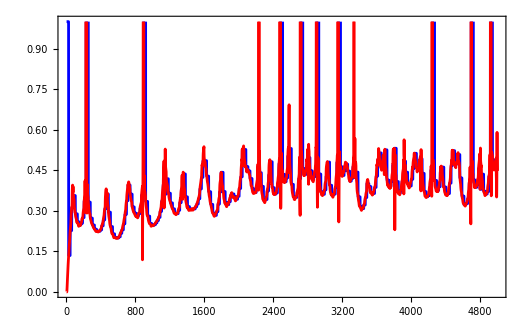

```mathematica
Show[{ListPlot[LabletData⟦All,3,6⟧,Joined-> True,PlotStyle-> Blue,PlotRange-> {0,1}],ListPlot[LabletData⟦All,3,7⟧,Joined-> True,PlotStyle-> Red,PlotRange->{0,1}]},PlotRange-> All,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},Frame-> True]
```

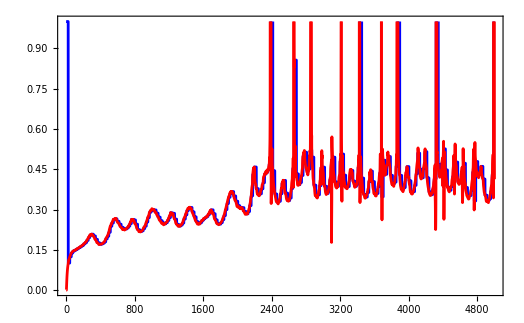

```mathematica
Show[{ListPlot[LabletData⟦All,4,6⟧,Joined-> True,PlotStyle-> Blue,PlotRange->{0,1}],ListPlot[LabletData⟦All,4,7⟧,Joined-> True,PlotStyle-> Red,PlotRange->{0,1}]},PlotRange-> All,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},Frame-> True]
```

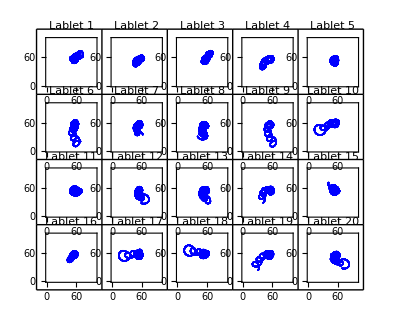

```mathematica
GraphicsGrid[Partition[Table[ListPlot[LabletData⟦All,i,1;;2⟧,PlotLabel-> "Lablet "<>ToString[i],PlotStyle-> Blue,PlotRange-> {{0,100},{0,100}},Frame-> True,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 9]}],{i,1,nop}],5],Frame-> All]
```

```mathematica
ListAnimate[Table[Show[{ListPlot[{LabletData⟦i,1,1;;2⟧},PlotStyle-> Red,PlotRange-> {{0,100},{0,100}},Frame-> True,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]}],ListPlot[{LabletData⟦i,2,1;;2⟧},PlotStyle-> Blue,PlotRange-> {{0,100},{0,100}},Frame-> True,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]}]}],{i,1,4999,10}],AnimationRunning-> False]
```